# Triplet state Population

## Fixed Kinematics Parameters

```mathematica
(* Display the Rate matrix and the relative triplet state population *)
Module[{R},
R[P_,g1_,g0_,gi_,k1_,k0_,ki_,ω_]:={
{-42.55-P 10-(g1+g0+gi),0,0,0,P 10},
{g1,-k1-ω,ω,0,0},
{g0,ω,-k0-2ω,ω,0},
{gi,0,ω,-ki-ω,0},
{42.55+P 10,k1,k0,ki,-P 10}};
Manipulate[
MatrixForm[{R[1,g0 α,g0,g0 α,0.0118,0.04,0.0118,ω]//MatrixForm,"","",
Table[Flatten[NullSpace[R[1,g0 α,g0,g0 α,0.0118,0.04,0.0118,ω]]][[i]],{i,2,4}]/Sum[Flatten[NullSpace[R[1,g0 α,g0,g0 α,0.0118,0.04,0.0118,ω]]][[i]],{i,2,4}] (* triplet state relative population *)
}],{{α,0.04657894737},0.01,0.1},{g0,0.1,1 },{ω,0,0.01}]]
```

```mathematica
(* Solve for ratio of g1:g0 such that N0:N+ = 72:12 *)
Module[{R},
R[P_,g1_,g0_,gi_,k1_,k0_,ki_,ω_]:={
{-42.55-P 10-(g1+g0+gi),0,0,0,P 10},
{g1,-k1-ω,ω,0,0},
{g0,ω,-k0-2ω,ω,0},
{gi,0,ω,-ki-ω,0},
{42.55+P 10,k1,k0,ki,-P 10}};
NSolve[
((Flatten[NullSpace[R[1,g0 α,g0,g0 α,0.0118,0.04,0.0118,0]]])[[3]])/((Flatten[NullSpace[R[1,g0 α,g0,g0 α,0.0118,0.04,0.0118,0]]])[[2]])==76/12
,{g0,α},Reals]
]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

{{α→0.0465789}}

```mathematica
(* clean up variable *)
Remove[k0,ki,g1,g0,gi,k1,R,P,W10,W0i,W1i];
```

```mathematica
(* in 10^6 s^-1*)
z={0,0,1,-1,0};
A=42;
W=12;
k1=0.011765;
k0=0.04;
ki=0.011765;
α={0.04657894737,0.2};
g0=0.055;
g1=g0 α[[2]];
gi=g0 α[[2]];
W10=0.005;
W0i=0.005;
W1i=0.00;
TripletSum={0,1,1,1,0};
(*R[P_]:={
{-A-P W-(g1+g0+gi),0,0,0,P W},
{g1,-k1-W10-W1i,W10,W1i,0},
{g0,W10,-k0-W10-W0i,W0i,0},
{gi,W1i,W0i,-ki-W0i-W1i,0},
{A+P W,k1,k0,ki,-P W}};*)
R[P_,ω_]:={
{-A-P W-(g1+g0+gi),0,0,0,P W},
{g1,-k1-ω-W1i,ω,W1i,0},
{g0,ω,-k0-ω-ω,ω,0},
{gi,W1i,ω,-ki-ω-W1i,0},
{A+P W,k1,k0,ki,-P W}};
R[P,ω]//MatrixForm
Table[Sum[R[P,ω][[i]][[j]],{i,1,5}],{j,1,5}]//Chop
Table[Flatten[NullSpace[R[1,0]]][[i]],{i,2,4}]/Sum[Flatten[NullSpace[R[1,0]]][[i]],{i,2,4}] (* triplet state relative population *)
```

(-42.077-12 P | 0 | 0 | 0 | 12 P
0.011 | -0.011765-ω | ω | 0. | 0
0.055 | ω | -0.04-2 ω | ω | 0
0.011 | 0. | ω | -0.011765-ω | 0
42+12 P | 0.011765 | 0.04 | 0.011765 | -12 P)

{0,0,0,0,0}

{0.288133,0.423735,0.288133}

```mathematica
1/0.01
```

100.

```mathematica
{"P=10",NumberForm[Eigenvalues[R[10,0]],4],
NumberForm[1/Eigenvalues[R[10,0]],4],
NullSpace[R[10,0]]}

{"P=0",NumberForm[Eigenvalues[R[0,0]],4],
NumberForm[1/Eigenvalues[R[0,0]],4],
NullSpace[R[0,0]]}

Manipulate[
TableForm[{
NumberForm[(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[2]],4]//Chop//FullSimplify (* equation for state m=1*),
NumberForm[(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[3]],4]//Chop//FullSimplify(* equation for state m=0*),
NumberForm[(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[4]],4]//Chop//FullSimplify(* equation for state m=-1*)}],{{P,1},0,10},{ω,0,0.001}]
(*Manipulate[
TableForm[{
NumberForm[(MatrixExp[td R[0]].MatrixExp[tp R[P]].{0,0,0,0,1})[[2]],4]//Chop//FullSimplify (* equation for state m=1*),
NumberForm[(MatrixExp[td R[0]].MatrixExp[tp R[P]].{0,0,0,0,1})[[3]],4]//Chop//FullSimplify(* equation for state m=0*),
NumberForm[(MatrixExp[td R[0]].MatrixExp[tp R[P]].{0,0,0,0,1})[[4]],4]//Chop//FullSimplify(* equation for state m=-1*)}],{{P,1},0,10}]//Chop*)
```

{P=10,{-282.,-0.06807,-0.01646,-0.01177,-3.1×10^-14},{-0.003546,-14.69,-60.76,-85.,-3.226×10^13},{{-0.393347,-0.36777,-0.540852,-0.36777,-0.53127}}}

Power::infy: Infinite expression 1/0. encountered.

{P=0,{-42.08,-0.04,-0.01177,-0.01177,0.},{-0.02377,-25.,-85.,-85.,ComplexInfinity},{{0.,0.,0.,0.,1.}}}

## Numerical

```mathematica
(* Normal mode Decay Rate *)
Manipulate[
TableForm[Transpose[{Round[Flatten[NullSpace[R[P,ω]]]/Total[Flatten[NullSpace[R[P,ω]]]],0.00001],
{"N_S","N_1","N_0","N_-1","N_G"},
Round[MatrixExp[t R[P,ω]].{0,0,0,0,1},0.00001]}]],{{P,1},0,10},{{t,50},0,300},{ω,0,0.005}]
```

```mathematica
(* Check population Sum *)
Manipulate[
Sum[(MatrixExp[t R[P]].{0,0,0,0,1})[[i]],{i,1,5}]
,{{P,1},0,10},{{t,50},0,300}]
```

```mathematica
(* Relative Triplet state population *)
```

```mathematica
Manipulate[Transpose[{{" ","N_1","N_0","N_-1"},
{"Rel Pop.",NumberForm[ ((MatrixExp[t R[P]].{0,0,0,0,1})[[2]])/(TripletSum.MatrixExp[t R[P]].{0,0,0,0,1}),3],NumberForm[((MatrixExp[t R[P]].{0,0,0,0,1})[[3]])/(TripletSum.MatrixExp[t R[P]].{0,0,0,0,1}),3],NumberForm[((MatrixExp[t R[P]].{0,0,0,0,1})[[4]])/(TripletSum.MatrixExp[t R[P]].{0,0,0,0,1}),3]},
{" ", "N_0/N_1","N_0/N_-1","Total Pop."},
{"Pop. Ratio",NumberForm[((MatrixExp[t R[P]].{0,0,0,0,1})[[3]])/((MatrixExp[t R[P]].{0,0,0,0,1})[[2]]),3],NumberForm[((MatrixExp[t R[P]].{0,0,0,0,1})[[3]])/((MatrixExp[t R[P]].{0,0,0,0,1})[[4]]),3],NumberForm[TripletSum.MatrixExp[t R[P]].{0,0,0,0,1},3]}}]//TableForm
,{{P,1},0,10},{{t,300},0,300}]
```

## Graphical

### Absolute population of Triplet state

```mathematica
Manipulate[
Plot[{
(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[2]],
(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[3]],
(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[4]],
z.MatrixExp[t R[P,ω]].{0,0,0,0,1}
},{t,0,150},PlotStyle->{Red,Green,Blue,Orange},PlotRange->{0,All},Epilog-> {Red,Text["N_0",{60,0.15 }],Text["N_1 and N_-1",{100,0.1}],Text["ΔN=N_0-N_-1",{42,0.1}]},
GridLines->{Table[40i,{i,0,10}],Automatic},
Frame->True,FrameLabel->{"time [μs]"," Population"},
AspectRatio->0.5, ImageSize->500
],{{P,1},0,10},{{ω,0},-0.01,0.01}]
```

```mathematica
Manipulate[Plot[
{(MatrixExp[t R[PP]].{0,0,0,0,1})[[2]],
(MatrixExp[t R[PP]].{0,0,0,0,1})[[3]],
(MatrixExp[t R[PP]].{0,0,0,0,1})[[4]],
z.MatrixExp[t R[PP]].{0,0,0,0,1}
},{PP,0,1},PlotStyle->{Red,Green,Blue,Orange},PlotRange->{0,All},
Epilog-> {
Text[{t},{6,(MatrixExp[250R[6]].{0,0,0,0,1})[[2]]+0.001 }],
{PointSize[Medium],Point[{0.25,400 β}],Point[{0.5,620 β}],Point[{1,950 β}]}
},ImageSize->400
,AxesLabel->{"Power"," Population"},AspectRatio->0.5],{{t,64},0,140},{β,0.00001,0.00010}]
```

```mathematica
Manipulate[Plot[
{(MatrixExp[t R[PP,ω]].{0,0,0,0,1})[[2]],
(MatrixExp[t R[PP,ω]].{0,0,0,0,1})[[3]],
(MatrixExp[t R[PP,ω]].{0,0,0,0,1})[[4]],
z.MatrixExp[t R[PP,ω]].{0,0,0,0,1}
},{PP,0,8},PlotStyle->{Red,Green,Blue,Orange},PlotRange->{0,All},
ImageSize->400,
(*Epilog-> {Text[{t},{6,(MatrixExp[250R[6]].{0,0,0,0,1})[[2]]+0.001 }]},*)AxesLabel->{"Power"," Population"},AspectRatio->0.5],{{t,50},0,140},{ω,0,0.01}]
```

```mathematica
(* the 1 cycle effect *)
Manipulate[Plot[
{If[t<tp,(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[1]],(MatrixExp[(t+tp) R[0 ,ω]].MatrixExp[tp R[P ,ω]].{0,0,0,0,1})[[1]]],
If[t<tp,(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[2]],(MatrixExp[(t-tp) R[0 ,ω]].MatrixExp[tp R[P ,ω]].{0,0,0,0,1})[[2]]],
If[t<tp,(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[3]],(MatrixExp[(t-tp) R[0 ,ω]].MatrixExp[tp R[P ,ω]].{0,0,0,0,1})[[3]]],
If[t<tp,(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[4]],(MatrixExp[(t-tp) R[0 ,ω]].MatrixExp[tp R[P ,ω]].{0,0,0,0,1})[[4]]],
If[t<tp,(MatrixExp[t R[P,ω]].{0,0,0,0,1})[[5]],(MatrixExp[(t-tp) R[0 ,ω]].MatrixExp[tp R[P,ω ]].{0,0,0,0,1})[[5]]],
If[t<tp,z.MatrixExp[t R[P,ω]].{0,0,0,0,1},z.MatrixExp[(t-tp) R[0,ω]].MatrixExp[tp R[P ,ω]].{0,0,0,0,1}]
},{t,0,200},PlotStyle->{Red, Orange, Green, Blue, Black,Purple},AxesLabel->{"time [μs]"," Population"},AspectRatio->0.5,ImageSize->600,PlotRange->{-0.2,0.5}],{{P,10},0,10},{{tp,80},0,200},{{ω,0},-0.01,0.01}]
```

## Simulation on Pulse cycle

```mathematica
(* Claim the electron polarization at n-th cycle *)
(* inital population of each pulse *)
η[n_,tp_,td_,P_,ω_]:=MatrixPower[MatrixExp[td R[0,ω]].MatrixExp[tp R[P,ω]],n].{0,0,0,0,1}
(*  population after laser pulse of each pulse *)
ρ[n_,tp_,td_,P_,ω_]:=MatrixExp[tp R[P,ω]].η[n,tp,td,P ,ω]
```

```mathematica
(* Numberical *)
Manipulate[
TableForm[Transpose[{η[n,tp,td,P,ω ],ρ[n,tp,td,P ,ω]}]]
,{{n,15},0,50,1},{{P,1},0,10},{{tp,50},0,300},{{td,260},0,300},{ω,0,0.01}]
```

```mathematica
(* Numberical *)
Manipulate[
TableForm[Transpose[{η[n,(α 1000)/f,(1-α)1000/f,P ,ω],ρ[n,(α 1000)/f,(1-α)1000/f,P,ω ]}]]
,{{n,15},0,20,1},{{P,1},0,10},{{α,0.2},0,1},{{f,1},0,10},{ω,0,0.01}]
```

```mathematica
(* N-depadance *)
Manipulate[
ListPlot[
{Table[{n,ρ[n,tp,td,P ,ω][[2]]},{n,0,10,1}],
Table[{n,ρ[n,tp,td,P ,ω][[3]]},{n,0,10,1}],
Table[{n,ρ[n,tp,td,P ,ω][[4]]},{n,0,10,1}]
},PlotRange->{0,All},PlotStyle->{Orange, Green, Blue}]
,{{P,1},0,10},{{tp,50},0,300},{{td,260},0,300},{ω,0,0.01}]
```

```mathematica
(* the n-th cycle *)
Manipulate[Plot[{
If[t<tp,(MatrixExp[t R[P,ω ]].η[n,tp,td,P ,ω])[[2]],
If[t<tp+td,(MatrixExp[(t-tp) R[0,ω ]].ρ[n,tp,td,P,ω ])[[2]]]],
If[t<tp,(MatrixExp[t R[P ,ω]].η[n,tp,td,P ,ω])[[3]],
If[t<tp+td,(MatrixExp[(t-tp) R[0,ω ]].ρ[n,tp,td,P,ω ])[[3]]]],
If[t<tp,(MatrixExp[t R[P,ω ]].η[n,tp,td,P ,ω])[[4]],
If[t<tp+td,(MatrixExp[(t-tp) R[0 ,ω]].ρ[n,tp,td,P ,ω])[[4]]]],
If[t<tp,z.MatrixExp[t R[P,ω ]].η[n,tp,td,P ,ω],
If[t<tp+td,z.MatrixExp[(t-tp) R[0,ω ]].ρ[n,tp,td,P,ω ]]]
},{t,0,(tp+td)},PlotStyle->{Red, Green, Blue,Orange},
GridLines->{Table[40i,{i,0,10}],Automatic},
Frame->True,FrameLabel->{"time [μs]"," Population"},
Epilog->{Text["N_0",{50,0.06}],Text["N_-1",{150,0.02 }],Text["ΔN=N_0-N_-1",{50,0.035}]},
PlotRange->All,ImageSize->500]
,{{n,50},0,50,10},{{P,0.1},0,4},{{tp,80},0,300},{{td,200},0,300},{{ω,0.0025},-0.01,0.01}]
```

```mathematica
Mag[P_,tp_,td_,n_,t_,ω_]:=If[t<tp,z.MatrixExp[t R[P,ω ]].η[n,tp,td,P ,ω],
If[t<tp+td,z.MatrixExp[(t-tp) R[0 ,ω]].ρ[n,tp,td,P ,ω]]]
```

```mathematica
(* the compare power *)
Manipulate[Plot[
{
Mag[0.25,tp,td,n,t,ω],Mag[0.5,tp,td,n,t,ω],Mag[1,tp,td,n,t,ω]
},{t,8,(tp+td)},PlotStyle->{Red, Green, Blue},GridLines->{Table[40i,{i,0,10}],Automatic},Frame->True,FrameLabel->{"time [μs]","Polarization"},PlotRange->All,
ImageSize->500, AspectRatio->0.5]
,{{n,50},{0,25,50}},{{tp,80},0,300},{{td,200},0,300},{{ω,0},-0.01,0.01}]
```

```mathematica
PopDiff[t_,tp_,td_,P_,n_]:=If[t<tp,z.MatrixExp[t R[P ]].η[n,tp,td,P ],
If[t<tp+td,z.MatrixExp[(t-tp) R[0 ]].ρ[n,tp,td,P ]]]
MD[tp_,td_,P_,n_]:=Table[{t,Mean[{PopDiff[t-8,tp,td,P,n],PopDiff[t+8,tp,td,P,n]}]},{t,16,tp+8,4}]
```

```mathematica
Table[8n,{n,0,30}]
```

{0,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240}

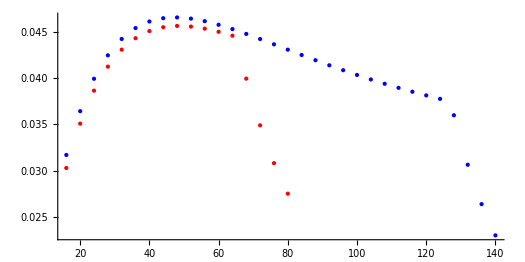

```mathematica
ListPlot[{MD[73,177,1,20],MD[135,365,1,20]},PlotRange->{{0,160},{0,All}},AspectRatio->0.5,PlotStyle->{Red,Blue},Ticks->{Table[8n,{n,0,30}]}]
```

```mathematica
(* the n-th cycle *)
Manipulate[Plot[
{
If[t<tp,(MatrixExp[t R[P ]].η[n,tp,td,P ])[[2]],
If[t<tp+td,(MatrixExp[(t-tp) R[0 ]].ρ[n,tp,td,P ])[[2]],
If[t<2tp+td,(MatrixExp[(t-tp-td) R[P ]].η[n+1,tp,td,P ])[[2]],
If[t<2(tp+td),(MatrixExp[(t-2tp-td) R[0 ]].ρ[n+1,tp,td,P ])[[2]]]]]],
If[t<tp,(MatrixExp[t R[P ]].η[n,tp,td,P ])[[3]],
If[t<tp+td,(MatrixExp[(t-tp) R[0 ]].ρ[n,tp,td,P ])[[3]],
If[t<2tp+td,(MatrixExp[(t-tp-td) R[P ]].η[n+1,tp,td,P ])[[3]],
If[t<2(tp+td),(MatrixExp[(t-2tp-td) R[0 ]].ρ[n+1,tp,td,P ])[[3]]]]]],
If[t<tp,(MatrixExp[t R[P ]].η[n,tp,td,P ])[[4]],
If[t<tp+td,(MatrixExp[(t-tp) R[0 ]].ρ[n,tp,td,P ])[[4]],
If[t<2tp+td,(MatrixExp[(t-tp-td) R[P ]].η[n+1,tp,td,P ])[[4]],
If[t<2(tp+td),(MatrixExp[(t-2tp-td) R[0 ]].ρ[n+1,tp,td,P ])[[4]]]]]],
If[t<tp,z.MatrixExp[t R[P ]].η[n,tp,td,P ],
If[t<tp+td,z.MatrixExp[(t-tp) R[0 ]].ρ[n,tp,td,P ],
If[t<2tp+td,z.MatrixExp[(t-tp-td) R[P ]].η[n+1,tp,td,P ],
If[t<2(tp+td),z.MatrixExp[(t-2tp-td) R[0 ]].ρ[n+1,tp,td,P ]]]]]
},{t,0,2(tp+td)},PlotStyle->{Red, Green, Blue,Orange},AxesLabel->{"time [μs]"," Population"},PlotRange->All,ImageSize->600]
,{{n,50},0,50,1},{{P,1},0,4},{{tp,80},0,300},{{td,170},0,300}]
```

```mathematica
(* Compare the decay part *)
Manipulate[Plot[
{
(z.MatrixExp[(t) R[0 ]].ρ[n,8.8,td,P ])(8.8+td),
(z.MatrixExp[(t) R[0 ]].ρ[n,23.2,td,P ])(23.2+td),
(z.MatrixExp[(t) R[0 ]].ρ[n,39,td,P ])(39+td),
(z.MatrixExp[(t) R[0 ]].ρ[n,59,td,P ])(59+td),
(z.MatrixExp[(t) R[0 ]].ρ[n,81,td,P ])(81+td),
(z.MatrixExp[(t) R[0 ]].ρ[n,100,td,P ])(100+td)
},{t,16,240},PlotStyle->{Red,Orange, Green,Cyan, Blue,Purple},GridLines->{Table[40i,{i,0,10}],Automatic},
Frame->True,FrameLabel->{"time [μs]","Polarization"},PlotRange->All,ImageSize->300]
,{{n,50},0,50,1},{{P,1},0,4},{{td,260},0,300}]
```

## On the Long term behaviour by all effect = Build up curve

```mathematica
Pe1[P_,tp_,td_]:=(ρ[50,tp,td,P ].{0,-1,1,0,0})/(ρ[50,tp,td,P ].{0,1,1,0,0})
Pe2[P_,tp_,td_]:=(ρ[50,tp,td,P ].{0,0,1,-1,0})/(ρ[50,tp,td,P ].{0,0,1,1,0})
Ne1[P_,tp_,td_]:=ρ[50,tp,td,P ].{0,1,1,0,0}
Ne2[P_,tp_,td_]:=ρ[50,tp,td,P ].{0,0,1,1,0}
PI1[P_,γ_,G_,tp_,td_,T_]:=(γ Ne1[P ,tp,td] 1000/(tp+td))/(γ Ne1[P ,tp,td] 1000/(tp+td)+G)Pe1[P ,tp,td](1-Exp[-T(γ Ne1[P ,tp,td] 1000/(tp+td)+G)])
PI2[P_,γ_,G_,tp_,td_,T_]:=(γ Ne2[P ,tp,td] 1000/(tp+td))/(γ Ne2[P ,tp,td] 1000/(tp+td)+G)Pe2[P ,tp,td](1-Exp[-T(γ Ne2[P ,tp,td] 1000/(tp+td)+G)])
```

```mathematica
(* Polarization VS Laser Power *)
Manipulate[Plot[{Pe1[P ,tp,1000/f-tp],Pe2[P ,tp,1000/f-tp]},{P,0,10},PlotStyle->{Cyan,Orange},PlotRange->All,AxesLabel->{"Power", "Pop.Diff."},AspectRatio->1],{{tp,80},0,300},{{f,1},0.1,10}]
```

```mathematica
Manipulate[Plot[{Pe1[P ,Duty/(f/1000),1000/f-Duty/(f/1000)],Pe2[P ,Duty/(f/1000),1000/f-Duty/(f/1000)]},{f,0.01,10},PlotStyle->{Orange,Cyan},PlotRange->{All}],{{P,1},0,10},{{Duty,0.05},0,1}]
```

```mathematica
Manipulate[Plot[(γ Ne2[P ,Duty/(f/1000),1000/f-Duty/(f/1000)]f +G),{f,0.01,10},PlotStyle->{Orange},PlotRange->{All}]
,{{P,1},0,10},{{Duty,0.05},0,1},{{γ,0.17},0,0.2},{{G,0.1},0,0.1},{{T,5},0,10}]
```

```mathematica
Manipulate[Plot[{Pe2[P ,Duty/(f/1000),1000/f-Duty/(f/1000)],Pe2[P ,Duty/(f/1000),1000/f-Duty/(f/1000)](1-Exp[-(γ Ne2[P ,Duty/(f/1000),1000/f-Duty/(f/1000)]f +G)T])},{f,0.01,10},PlotStyle->{Orange,Cyan},PlotRange->{All}],{{P,1},0,10},{{Duty,0.05},0,1},{{γ,0.17},0,0.2},{{G,0.1},0,0.1},{{T,5},0,10}]
```

```mathematica
(* the polarization for difference duty and frequency for N0 <-> N- transition *)
Manipulate[
Plot[{
PI2[P ,γ,G,0.05/(f/1000),1000/f-0.05/(f/1000),T],
PI2[P ,γ,G,0.10/(f/1000),1000/f-0.10/(f/1000),T],
PI2[P ,γ,G,0.15/(f/1000),1000/f-0.15/(f/1000),T],
PI2[P ,γ,G,0.20/(f/1000),1000/f-0.20/(f/1000),T],
PI2[P ,γ,G,0.30/(f/1000),1000/f-0.30/(f/1000),T],
PI2[P ,γ,G,0.40/(f/1000),1000/f-0.40/(f/1000),T],
PI2[P ,γ,G,0.50/(f/1000),1000/f-0.50/(f/1000),T]}
,{f,0,10},PlotStyle->{Red, Orange,Brown,Green,Cyan,Blue, Purple},PlotRange->All,(*Epilog-> {Text[{P},{5,0.00003}]},*)AxesLabel->{"Freq[kHz]", "Pop. Diff."},(*AspectRatio->Automatic,*)ImageSize->500]
,{{P,1},0,10},{{γ,0.1},0,1},{{G,0.01},0,1},{{T,3},0,10}]
```

```mathematica
(* the polarization for difference duty and frequency for N+ <-> N0 transition *)
Manipulate[
Plot[{
PI1[P ,γ,G,0.05/(f/1000),1000/f-0.05/(f/1000),T],
PI1[P ,γ,G,0.10/(f/1000),1000/f-0.10/(f/1000),T],
PI1[P ,γ,G,0.20/(f/1000),1000/f-0.20/(f/1000),T],
PI1[P ,γ,G,0.30/(f/1000),1000/f-0.30/(f/1000),T],
PI1[P ,γ,G,0.40/(f/1000),1000/f-0.40/(f/1000),T],
PI1[P ,γ,G,0.50/(f/1000),1000/f-0.50/(f/1000),T]}
,{f,0,10},PlotStyle->{Red, Orange,Brown,Green,Cyan,Blue, Purple},PlotRange->All,Epilog-> {Text[{P},{5,0.00003}]},AxesLabel->{"Freq[kHz]", "Pop. Diff."},(*AspectRatio->1,*)ImageSize->500]
,{{P,1},0,10},{{γ,0.1},0,1},{{G,0.01},0,1},{{T,3},0,10}]
```